## Distribucion de Porbabilidad a partir de una funcion dada

```mathematica
?G*Distribution
```

```mathematica
GompertzDist=ProbabilityDistribution[b η Exp[η + b x -η Exp[b x]],{x,0,∞},Assumptions->{η>0,b>0}]
```

ProbabilityDistribution[b ⅇ^(x b+η-ⅇ^(x b) η) η,{x,0,∞},Assumptions→{η>0,b>0}]

```mathematica
PDF[GompertzDist,x]
```

Piecewise[{{b ⅇ^(b x+η-ⅇ^(b x) η) η, x>0}, {0, True}}]

```mathematica
CDF[GompertzDist,x]
```

Piecewise[{{1-ⅇ^(η-ⅇ^(b x) η), x>0}, {0, True}}]

```mathematica
Mean[GompertzDist]
```

(ⅇ^η Gamma[0,η])/b

```mathematica
Median[GompertzDist]
```

Log[(η+Log[2])/η]/b

```mathematica
Variance[GompertzDist]
```

-(ⅇ^η (ⅇ^η Gamma[0,η]^2-2 MeijerG[{{},{1,1}},{{0,0,0},{}},η]))/b^2

```mathematica
Moment[GompertzDist,2]
```

Moment[ProbabilityDistribution[b ⅇ^(x b+η-ⅇ^(x b) η) η,{x,0,∞},Assumptions→{η>0,b>0}],2]

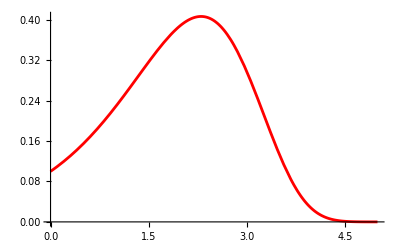

```mathematica
g1=Plot[PDF[GompertzDist,x]/.{η->0.1,b->1},{x,0,5},PlotStyle->Red]
```

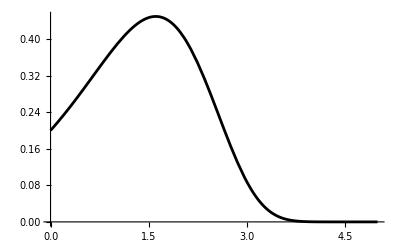

```mathematica
g2=Plot[PDF[GompertzDist,x]/.{η->.2,b->1.},{x,0,5},PlotStyle->Black,PlotRange->All]
```

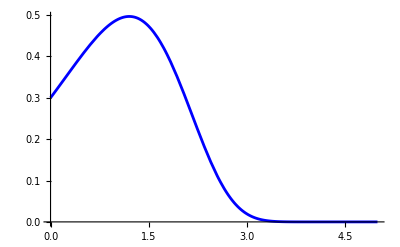

```mathematica
g3=Plot[PDF[GompertzDist,x]/.{η->.3,b->1.},{x,0,5},PlotStyle->Blue,PlotRange->All]
```

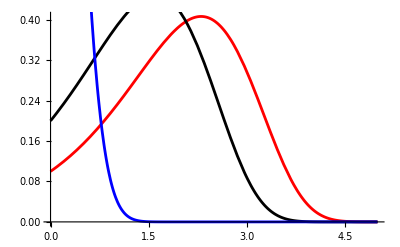

```mathematica
Show[g1,g2,g3,Pl]
```

```mathematica
CDF[GompertzDist,x]/.{η->0.1,b->1.}
```

Piecewise[{{1-ⅇ^(0.1-0.1 ⅇ^(1. x)), x>0}, {0, True}}]

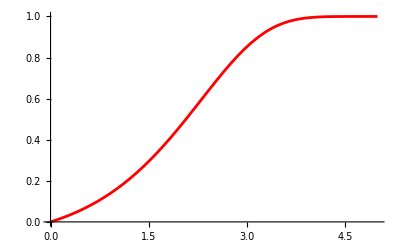

```mathematica
g4=Plot[1-ⅇ^(0.1-0.1 ⅇ^(1. x)),{x,0,5},PlotStyle->Red]
```

```mathematica
RandomVariate[GompertzDist/.{η->0.1,b->1.},100]
```

RandomVariate::noimp: Sampling from ProbabilityDistribution[0.1 ⅇ^(0.1+1. x-0.1 ⅇ^(1. x)),{x,0,∞},Assumptions→{True,True}] is not implemented.

RandomVariate[ProbabilityDistribution[0.1 ⅇ^(0.1+1. x-0.1 ⅇ^(1. x)),{x,0,∞},Assumptions→{True,True}],100]

```mathematica
Clear@GompertzDist2
```

```mathematica
GompertzDist2[η_/;η>0,b_/;b>0]=ProbabilityDistribution[b η Exp[η + b x -η Exp[b x]],{x,0,∞}]
```

ProbabilityDistribution[b ⅇ^(x b+η-ⅇ^(x b) η) η,{x,0,∞}]

```mathematica
RandomVariate[GompertzDist2[0.1,1.],5]
```

{2.39611,1.1671,2.21582,3.49866,1.79899}

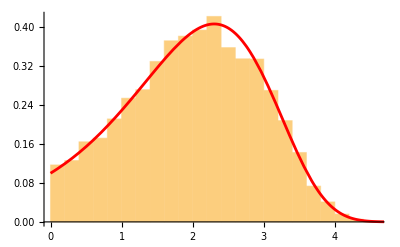

```mathematica
Show[Histogram[RandomVariate[GompertzDist2[0.1,1.],10000],Automatic,"PDF"],g1]
```

## Generate data with errors, OLS vs MLE

```mathematica
IntegerPart@AbsoluteTime[]
```

3939872133

```mathematica
SeedRandom[IntegerPart@AbsoluteTime[]];
```

```mathematica
error=1.;
dat=Table[{x,5.x-3.+ RandomVariate[NormalDistribution[0,error]]},{x,0,3,.1}];
```

```mathematica
Length@dat
```

31

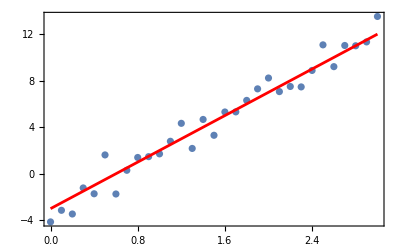

```mathematica
Show[ListPlot[dat,Axes->False],Plot[5.x-3.,{x,0,3},PlotStyle->Red,Axes->False],Frame->True]
```

```mathematica
Dimensions@dat
```

{31,2}

## OLS (Ordinary Least Squares)

```mathematica
Clear[modelo]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
mincuad=Sum[(dat[[k,2]]-modelo[dat[[k,1]]])^2,{k,Length@dat}]
```

(-4.13966-b)^2+(13.5187-3. a-b)^2+(11.3315-2.9 a-b)^2+(10.999-2.8 a-b)^2+(11.0241-2.7 a-b)^2+(9.20466-2.6 a-b)^2+(11.0773-2.5 a-b)^2+(8.8785-2.4 a-b)^2+(7.46298-2.3 a-b)^2+(7.50112-2.2 a-b)^2+(7.05963-2.1 a-b)^2+(8.22786-2. a-b)^2+(7.29565-1.9 a-b)^2+(6.30384-1.8 a-b)^2+(5.31756-1.7 a-b)^2+(5.30774-1.6 a-b)^2+(3.30557-1.5 a-b)^2+(4.66586-1.4 a-b)^2+(2.17456-1.3 a-b)^2+(4.33295-1.2 a-b)^2+(2.78906-1.1 a-b)^2+(1.708-1. a-b)^2+(1.46789-0.9 a-b)^2+(1.39728-0.8 a-b)^2+(0.296811-0.7 a-b)^2+(-1.74102-0.6 a-b)^2+(1.61727-0.5 a-b)^2+(-1.72162-0.4 a-b)^2+(-1.22101-0.3 a-b)^2+(-3.46088-0.2 a-b)^2+(-3.14374-0.1 a-b)^2

```mathematica
mincuad//FullSimplify
```

31. (43.1946+3.05 a^2+(-8.95727+b) b+a (-21.8868+3. b))

```mathematica
AbsoluteTiming[solOLS=NMinimize[mincuad,{a,b}]]
```

{0.003667,{25.373,{a→5.28181,b→-3.44408}}}

```mathematica
AbsoluteTiming[solOLS=FindMinimum[mincuad,{a,b},Method->"LevenbergMarquardt"]]
```

{0.004057,{25.373,{a→5.28181,b→-3.44408}}}

```mathematica
AbsoluteTiming[otraSol=Fit[dat, {1,x},x]]
```

{0.002227,-3.44408+5.28181 x}

```mathematica
eca=D[mincuad,a];
ecb=D[mincuad,b];
```

```mathematica
Solve[{eca==0,ecb==0},{a,b}]
```

{{a→5.28181,b→-3.44408}}

```mathematica
solOLS[[2]]
```

{a→5.28181,b→-3.44408}

```mathematica
modelo[x]/.solOLS[[2]]
```

-3.44408+5.28181 x

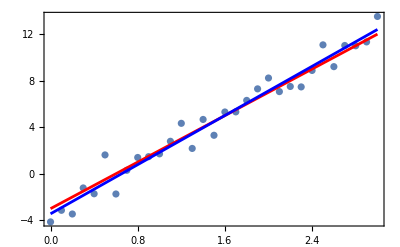

```mathematica
Show[ListPlot[dat,Axes->False],Plot[5.x-3.,{x,0,3},PlotStyle->Red,Axes->False],Plot[modelo[x]/.solOLS[[2]],{x,0,3},PlotStyle->Blue,Axes->False],Frame->True]
```

## MLE (Maximum Likelihood Estimator)

```mathematica
Clear[modelo,dist]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
dist[y_,x_]=PDF[NormalDistribution[modelo[x],σ],y]
```

(ⅇ^(-(-b-a x+y)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]
```

1/(32768 √2 π^(31/2) σ^31)ⅇ^(-(-4.13966-b)^2/(2 σ^2)-(13.5187-3. a-b)^2/(2 σ^2)-(11.3315-2.9 a-b)^2/(2 σ^2)-(10.999-2.8 a-b)^2/(2 σ^2)-(11.0241-2.7 a-b)^2/(2 σ^2)-(9.20466-2.6 a-b)^2/(2 σ^2)-(11.0773-2.5 a-b)^2/(2 σ^2)-(8.8785-2.4 a-b)^2/(2 σ^2)-(7.46298-2.3 a-b)^2/(2 σ^2)-(7.50112-2.2 a-b)^2/(2 σ^2)-(7.05963-2.1 a-b)^2/(2 σ^2)-(8.22786-2. a-b)^2/(2 σ^2)-(7.29565-1.9 a-b)^2/(2 σ^2)-(6.30384-1.8 a-b)^2/(2 σ^2)-(5.31756-1.7 a-b)^2/(2 σ^2)-(5.30774-1.6 a-b)^2/(2 σ^2)-(3.30557-1.5 a-b)^2/(2 σ^2)-(4.66586-1.4 a-b)^2/(2 σ^2)-(2.17456-1.3 a-b)^2/(2 σ^2)-(4.33295-1.2 a-b)^2/(2 σ^2)-(2.78906-1.1 a-b)^2/(2 σ^2)-(1.708-1. a-b)^2/(2 σ^2)-(1.46789-0.9 a-b)^2/(2 σ^2)-(1.39728-0.8 a-b)^2/(2 σ^2)-(0.296811-0.7 a-b)^2/(2 σ^2)-(-1.74102-0.6 a-b)^2/(2 σ^2)-(1.61727-0.5 a-b)^2/(2 σ^2)-(-1.72162-0.4 a-b)^2/(2 σ^2)-(-1.22101-0.3 a-b)^2/(2 σ^2)-(-3.46088-0.2 a-b)^2/(2 σ^2)-(-3.14374-0.1 a-b)^2/(2 σ^2))

```mathematica
Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]//PowerExpand
```

-(-4.13966-b)^2/(2 σ^2)-(13.5187-3. a-b)^2/(2 σ^2)-(11.3315-2.9 a-b)^2/(2 σ^2)-(10.999-2.8 a-b)^2/(2 σ^2)-(11.0241-2.7 a-b)^2/(2 σ^2)-(9.20466-2.6 a-b)^2/(2 σ^2)-(11.0773-2.5 a-b)^2/(2 σ^2)-(8.8785-2.4 a-b)^2/(2 σ^2)-(7.46298-2.3 a-b)^2/(2 σ^2)-(7.50112-2.2 a-b)^2/(2 σ^2)-(7.05963-2.1 a-b)^2/(2 σ^2)-(8.22786-2. a-b)^2/(2 σ^2)-(7.29565-1.9 a-b)^2/(2 σ^2)-(6.30384-1.8 a-b)^2/(2 σ^2)-(5.31756-1.7 a-b)^2/(2 σ^2)-(5.30774-1.6 a-b)^2/(2 σ^2)-(3.30557-1.5 a-b)^2/(2 σ^2)-(4.66586-1.4 a-b)^2/(2 σ^2)-(2.17456-1.3 a-b)^2/(2 σ^2)-(4.33295-1.2 a-b)^2/(2 σ^2)-(2.78906-1.1 a-b)^2/(2 σ^2)-(1.708-1. a-b)^2/(2 σ^2)-(1.46789-0.9 a-b)^2/(2 σ^2)-(1.39728-0.8 a-b)^2/(2 σ^2)-(0.296811-0.7 a-b)^2/(2 σ^2)-(-1.74102-0.6 a-b)^2/(2 σ^2)-(1.61727-0.5 a-b)^2/(2 σ^2)-(-1.72162-0.4 a-b)^2/(2 σ^2)-(-1.22101-0.3 a-b)^2/(2 σ^2)-(-3.46088-0.2 a-b)^2/(2 σ^2)-(-3.14374-0.1 a-b)^2/(2 σ^2)-(31 Log[2])/2-(31 Log[π])/2-31 Log[σ]

```mathematica
Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]//PowerExpand//FullSimplify
```

(-669.517-47.275 a^2+a (339.245-46.5 b)+(138.838-15.5 b) b-28.4871 σ^2-31. σ^2 Log[σ])/σ^2

```mathematica
lmle1=PowerExpand[Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]]//FullSimplify
```

(-669.517-47.275 a^2+a (339.245-46.5 b)+(138.838-15.5 b) b-28.4871 σ^2-31. σ^2 Log[σ])/σ^2

```mathematica
AbsoluteTiming[solMLE=NMaximize[{lmle1,σ>0},{a,b,σ}]]
```

{0.064981,{-40.8824,{a→5.28181,b→-3.44408,σ→0.904702}}}

```mathematica
(a/.solOLS[[2]])-(a/.solMLE[[2]])
```

-2.66454×10^-15

```mathematica
Chop[%]
```

0

```mathematica
(b/.solOLS[[2]])-(b/.solMLE[[2]])
```

5.77316×10^-15

```mathematica
Chop[%]
```

0

### Otra forma de la distribución de errores

```mathematica
Clear[a,b,modelo]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
dist[y_,x_]=PDF[StudentTDistribution[modelo[x],σ,Length@dat -2],y]
```

(9984397484360291143009697792 √29)/(5014575 π (29+(-b-a x+y)^2/σ^2)^15 σ)

```mathematica
lmle1=PowerExpand[Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]]//FullSimplify;
```

```mathematica
AbsoluteTiming[solMLE=NMaximize[{lmle1,a>0&&σ>0},{a,b,σ}]]
```

{1.53054,{-40.9283,{a→5.29403,b→-3.47605,σ→0.87698}}}

```mathematica
(a/.solOLS[[2]])-(a/.solMLE[[2]])
```

-0.0122253

```mathematica
(b/.solOLS[[2]])-(b/.solMLE[[2]])
```

0.0319717

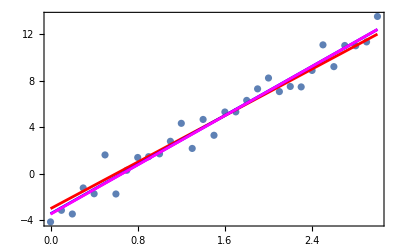

```mathematica
Show[ListPlot[dat,Axes->False],Plot[5.x-3.,{x,0,3},PlotStyle->Red,Axes->False],Plot[modelo[x]/.solOLS[[2]],{x,0,3},PlotStyle->Blue,Axes->False],Plot[modelo[x]/.solMLE[[2]],{x,0,3},PlotStyle->Magenta,Axes->False],Frame->True]
```

## Kernel Density Estimation (https://en.wikipedia.org/wiki/Kernel_density_estimation)

Kernel Normal

```mathematica
Clear@f
```

```mathematica
f[x_,xi_,h_,σ_,n_]:=1/(n h σ) 1/(√(2 π))Sum[Exp[-(x-xi[[k]])^2/(2 h^2 σ^2)],{k,n}]
```

```mathematica
n=25;
```

```mathematica
dat=RandomVariate[StudentTDistribution[5],n];
```

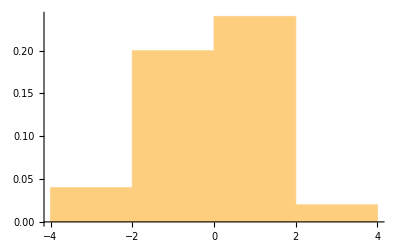

```mathematica
grh=Histogram[dat,Automatic,"PDF"]
```

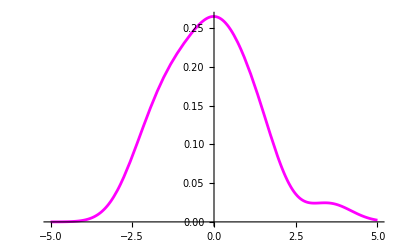

```mathematica
grkde=Plot[f[x,dat,.5,StandardDeviation[dat],Length@dat],{x,-5,5},PlotStyle->Magenta]
```

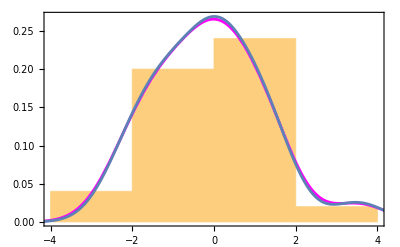

```mathematica
Show[grh,grkde,SmoothHistogram[dat],Frame->True]
```

```mathematica
kde=SmoothKernelDistribution[dat,Automatic,"Epanechnikov"]
```

DataDistribution[…]

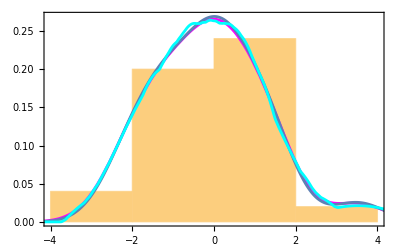

```mathematica
Show[grh,grkde,SmoothHistogram[dat],Plot[PDF[kde,x],{x,-5,5},PlotStyle->Cyan],Frame->True]
```

```mathematica
FindDistribution[dat]
```

NormalDistribution[-0.0565974,1.51965]

```mathematica
FindDistribution[dat, TargetFunctions->{StudentTDistribution}]
```

StudentTDistribution[-0.134879,1.26363,19.996]

```mathematica
FindDistribution[dat,5]
```

{NormalDistribution[-0.0565974,1.51965],UniformDistribution[{-2.32081,3.5216}],WeibullDistribution[1.66059,2.82029,-2.58729],LogisticDistribution[-0.138034,0.858585],StudentTDistribution[-0.0847648,1.46812,29.5562]}

## Exoplanetas

```mathematica
Directory[]
```

/Users/michel

```mathematica
NotebookDirectory[]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
Directory[]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
exopl=Import["exoplanetas-11-2024.csv"];
```

```mathematica
Length@exopl
```

7345

```mathematica
header=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_measurement_type,radius_measurement_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
Counts@exopl[[All,2]]
```

<|planet_status→1,Confirmed→7344|>

```mathematica
masas=Select[exopl[[All,3]],NumberQ];
```

```mathematica
Length@masas
```

4386

```mathematica
distmasas=SmoothKernelDistribution[Log10@masas]
```

DataDistribution[…]

```mathematica
10^Mean@distmasas
```

1.30675

```mathematica
Log10@Min[masas]
```

-4.20066

10^(-4.20066 ) jupiter mass in earth mass

WolframAlphaQueryResults

```mathematica
Sort[masas][[1;;10]]
```

{0.000063,0.00007,0.00019,0.00021,0.00076,0.00082,0.0009,0.00091,0.001041,0.00107}

```mathematica
Reverse[Sort[masas]][[1;;10]]
```

{74.6,73.4,72.07,72.,72.,71.7,71.64,71.12,71.03,70.69}

```mathematica
Max[masas]
```

74.6

```mathematica
Min[masas]
```

0.000063

```mathematica
Log10@Max[masas]
```

1.87274

```mathematica
Log10@Min[masas]
```

-4.20066

Mass Moon / mass Earth

WolframAlphaQueryResults

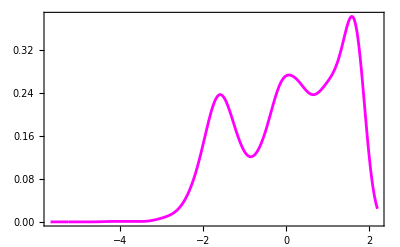

```mathematica
grma=Plot[PDF[distmasas,m],{m,-5.68,2.2},Frame->True,Axes->False,PlotStyle->Magenta]
```

grafico con datos del año pasado

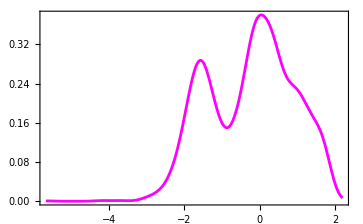

```mathematica
FindDistribution[Log10@masas]
```

MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}]

```mathematica
fdist=FindDistribution[Log10@masas,5]
```

{MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}],MixtureDistribution[{0.143155,0.532003,0.324841},{NormalDistribution[-1.5713,0.245506],NormalDistribution[0.710644,0.723507],UniformDistribution[{-4.28793,1.95038}]}],NormalDistribution[0.117122,1.25613],StudentTDistribution[0.146324,1.22999,4771.72],LogisticDistribution[0.223105,0.732639]}

```mathematica
%//TableForm
```

MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}]
MixtureDistribution[{0.143155,0.532003,0.324841},{NormalDistribution[-1.5713,0.245506],NormalDistribution[0.710644,0.723507],UniformDistribution[{-4.28793,1.95038}]}]
NormalDistribution[0.117122,1.25613]
StudentTDistribution[0.146324,1.22999,4771.72]
LogisticDistribution[0.223105,0.732639]

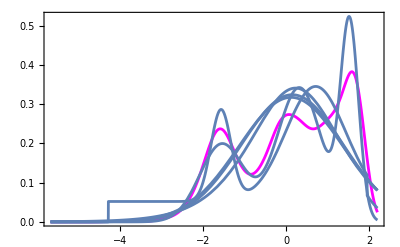

```mathematica
Show[grma,Plot[Table[PDF[fdist[[k]],lgm],{k,5}],{lgm,-5.68,2.2}],PlotRange->All]
```

```mathematica
fdist[[1]]
```

MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}]

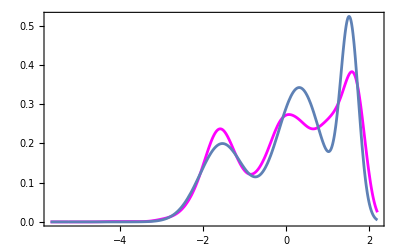

```mathematica
Show[grma,Plot[PDF[fdist[[1]],lgm],{lgm,-5.68,2.2}],PlotRange->All]
```